# Ejercicio I.2: Representación gráfica de una red

## Nombre del Alumno: Felix Sanz Gonzalez DNI: 78997168b

```mathematica
Clear["Global`*"]
```

# 1.- Construir grafo de una cola SIMPLE

```mathematica
SetAttributes[createPrimitive,HoldAll]

createPrimitive[patt_,expr_]:=Typeset`MakeBoxes[p:patt,fmt_,Graphics]:=Typeset`MakeBoxes[Interpretation[expr,p],fmt,Graphics]
```

```mathematica
a=createPrimitive[face[x_: 0.1],
{Circle[{1.5 x,0},x],Line[{{-x,x},{0,x},{0,-x},{-x,-x}}],Line[{{0,0},{x/2,0}}]
}]
```

```mathematica
MakeBoxes[Interpretation[expr,p]]//DisplayForm
```

expr

```mathematica
InterpretationBox["expr",p]//DisplayForm
```

expr

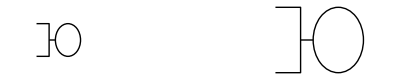

```mathematica
g=Show[Graphics[face[]],Graphics[Translate[face[0.2],{2,0}]]]
```

# 2.- Construir una topología gráfica de red

```mathematica
GraphPlot[{1->5,1->2,2->3,2->4,5->2,5->4,4->3},DirectedEdges->True,VertexLabeling->True,]
```

GraphPlot::argx: GraphPlot called with 4 arguments; 1 argument is expected.

GraphPlot[{1→5,1→2,2→3,2→4,5→2,5→4,4→3},DirectedEdges→True,VertexLabeling→True,Null]

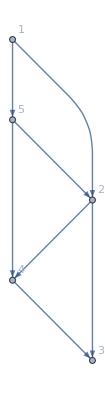

```mathematica
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4},DirectedEdges->True,VertexLabeling->True]
```

```mathematica
arrow=Graphics[face[0.01]];
```

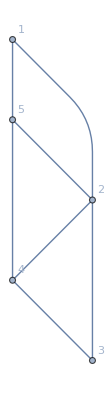
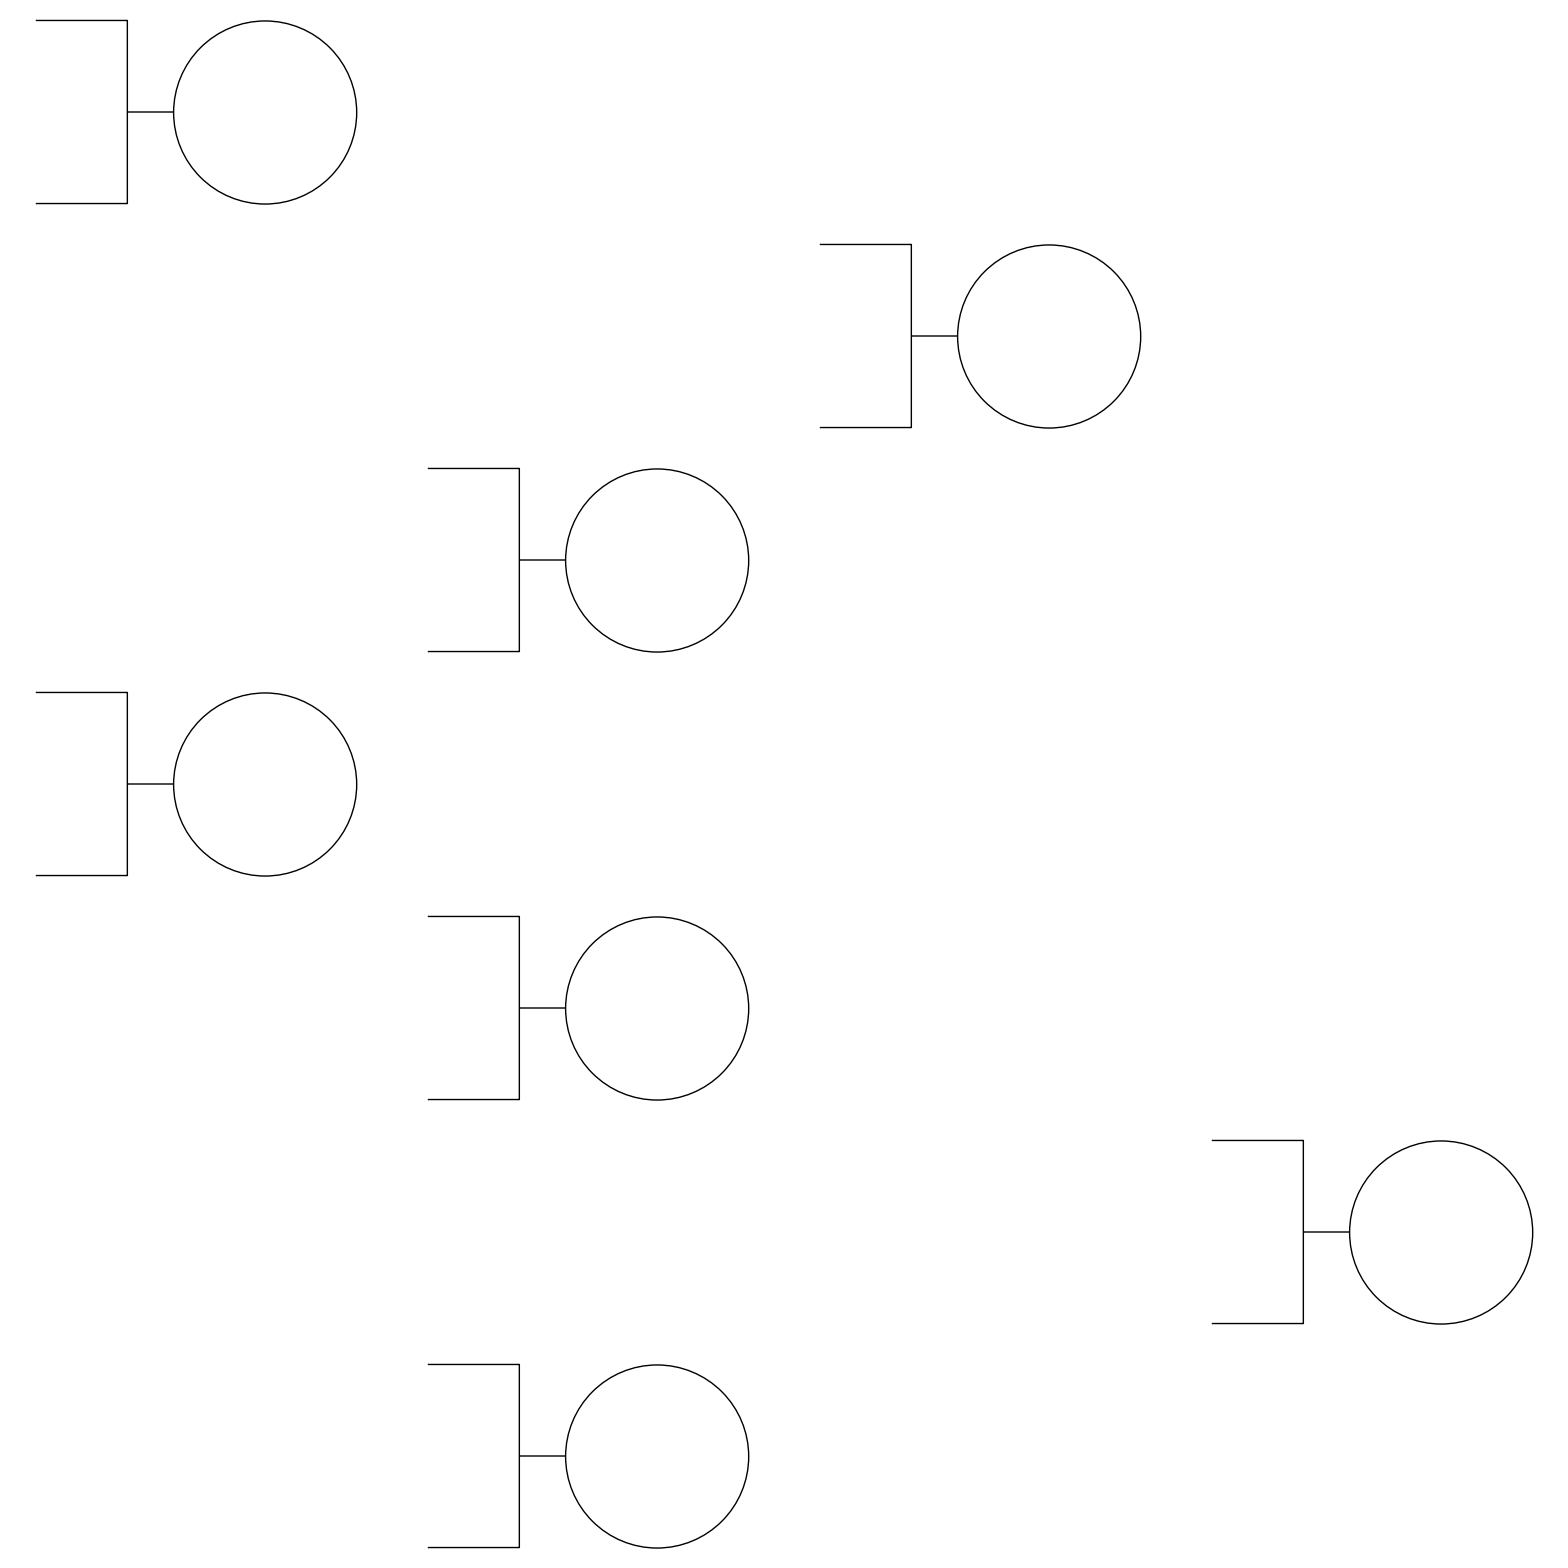

```mathematica
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4},DirectedEdges->True,VertexLabeling->True,EdgeRenderingFunction->({Line[#],Inset[arrow,Mean[#1],Automatic,0.3,#[[2]]-#[[1]],Background->White]}&)]
```

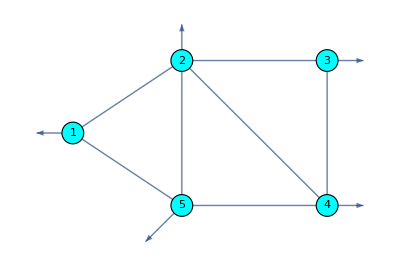
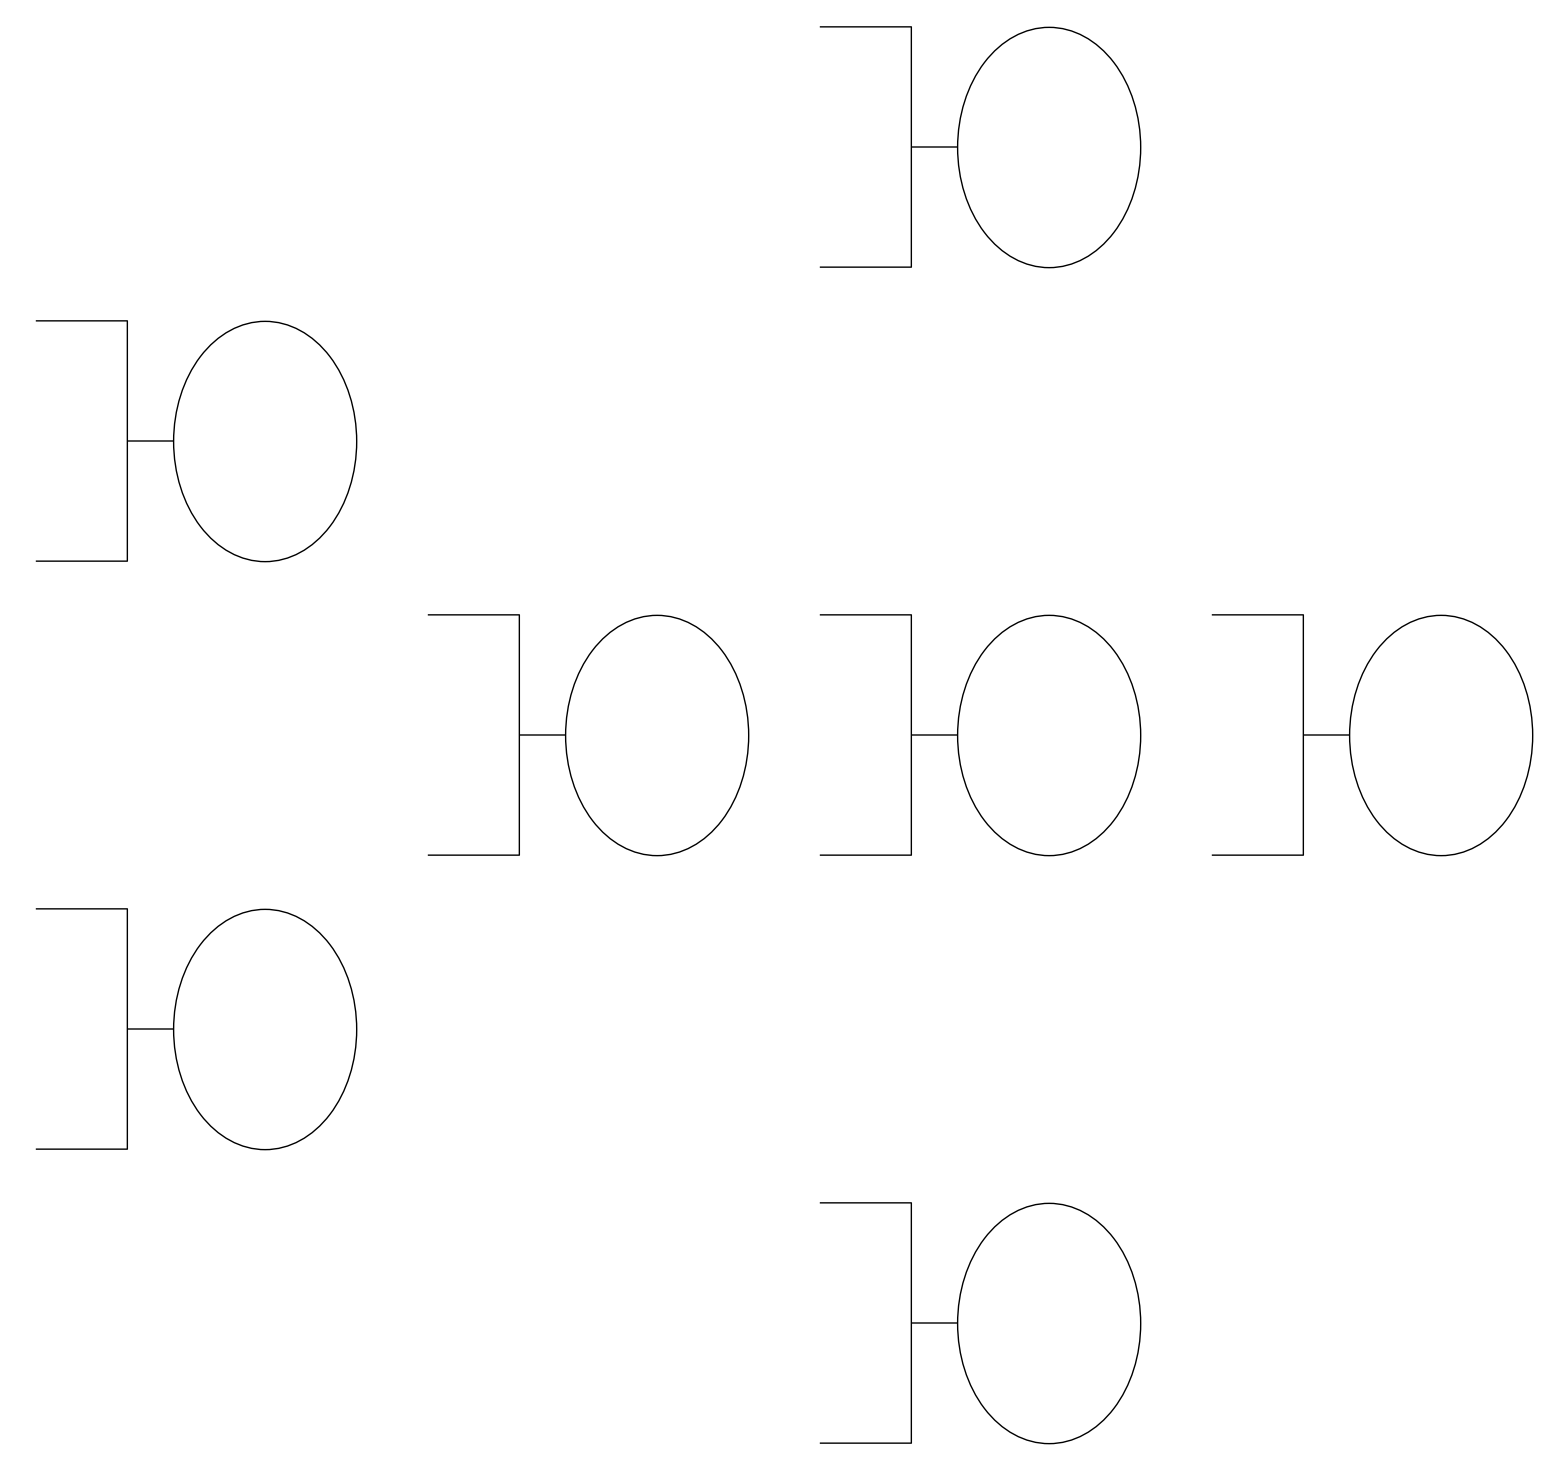

```mathematica
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4,10->1,6->5,7->2,4->8,3->9},VertexCoordinateRules->{1->{0.5,0},2->{2,1},3->{4,1},4->{4,-1},5->{2,-1},6->{1.5,-1.5},7->{2,1.5},8->{4.5,-1},9->{4.5,1},10->{0,0}},VertexRenderingFunction->(If[#2≤5,{EdgeForm[Black],Cyan,Disk[#1,0.15],Black,Text[#2,#1]}]&),EdgeRenderingFunction-> (If[#2[[1]]≤5&&#2[[2]]≤5,{{Arrowheads[{0,.03,0,.03,.03}],Arrow[#1]},Inset[arrow,Mean[#1],Automatic,0.5,#[[2]]-#[[1]],Background->White]},{Arrowheads[{0,.03,.03}],Arrow[#1]}]&)
]
```

# 3.- Adaptar la topología de red física a una red de colas equivalente

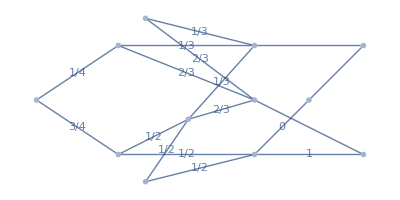

```mathematica
GraphPlot[{{{1,5}->{5,2},"1/2"},{{1,5}->{5,4},"1/2"},{{1,2}->{2,3},"1/3"},{{1,2}->{2,4},"2/3"},{{5,2}->{2,3},"1/3"},{{5,2}->{2,4},"2/3"},{{2,2}->{2,3},"1/3"},{{2,2}->{2,4},"2/3"},{{1,1}->{1,2},"1/4"},{{1,1}->{1,5},"3/4"},{{5,5}->{5,2},"1/2"},{{5,5}->{5,4},"1/2"},{2,4}->{4,4},{{5,4}->{4,4},"1"},{2,3}->{3,3},{{5,4}->{4,3},"0"},{4,3}->{3,3}},

VertexCoordinateRules->{{1,1}->{0,0},{1,2}->{1.5,1},{1,5}->{1.5,-1},{2,4}->{4,0},{5,5}->{2,-1.5},{2,3}->{4,1},{5,4}->{4,-1},{3,3}->{6,1},{4,4}->{6,-1},{2,2}->{2,1.5},{4,3}->{5,0}},VertexRenderingFunction-> ({Inset[arrow,#,Automatic,If[#2[[1]]==#2[[2]],0.2,0.5],If[#2=={5,2},{1,0.8},If[#2=={2,4},{2,-1},If[#2=={4,3},{1,1},{1,0}]]],Background->White]}&)
]
```

# 4.- Implementación del ejercicio con Queueing networks y sin protocolo

```mathematica
λ=2000; μ={3000,3000,3000,3000,3000,3000,3000,99999,99999};
```

```mathematica
γ={ (*Indicamos el caudal debido a los traficos externos que entran de forma directa*)
λ*1/4,(*Enlace A*)
λ*3/4,(*Enlace B*)
λ*1/2,(*Enlace C*)
λ*1/2,(*Enlace D*)
λ*1/3,(*Enlace E*)
λ*2/3,(*Enlace F*)
0,(*Enlace G*)
0,(*Enlace H*)
0   (*Enlace I*)
};

r={
{0,0,0,0,1/3,2/3,0,0,0}, (*Enlace A*)
{0,0,1/2,1/2,0,0,0,0,0}, (*Enlace B*)
{0,0,0,0,1/3,2/3,0,0,0}, (*Enlace C*)
{0,0,0,0,0,0,0,1,0}, (*Enlace D*)
{0,0,0,0,0,0,0,0,1}, (*Enlace E*)
{0,0,0,0,0,0,0,1,0},(*Enlace F*)
{0,0,0,0,0,0,0,0,1},(*Enlace G*)
{0,0,0,0,0,0,0,0,0},(*Enlace H*)
{0,0,0,0,0,0,0,0,0}    (*Enlace I*)
};

c={1,1,1,1,1,1,1,1,1};
𝒩=QueueingNetworkProcess[γ,r,μ,c];
```

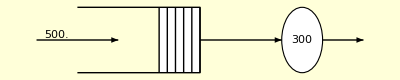
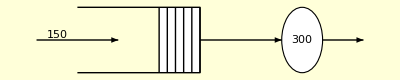
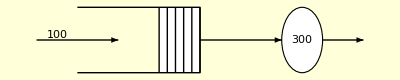
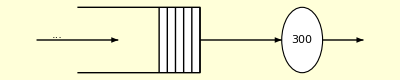
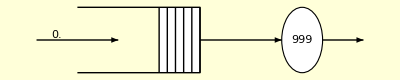
{-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 1.
Performance Measures | 
MeanSystemSize | 0.2
MeanSystemTime | 0.0004
MeanQueueSize | 0.0333333
MeanQueueTime | 0.0000666667,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 2.
Performance Measures | 
MeanSystemSize | 1.
MeanSystemTime | 0.000666667
MeanQueueSize | 0.5
MeanQueueTime | 0.000333333,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 3.
Performance Measures | 
MeanSystemSize | 1.4
MeanSystemTime | 0.0008
MeanQueueSize | 0.816667
MeanQueueTime | 0.000466667,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 4.
Performance Measures | 
MeanSystemSize | 1.4
MeanSystemTime | 0.0008
MeanQueueSize | 0.816667
MeanQueueTime | 0.000466667,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 5.
Performance Measures | 
MeanSystemSize | 0.894737
MeanSystemTime | 0.000631579
MeanQueueSize | 0.422515
MeanQueueTime | 0.000298246,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 6.
Performance Measures | 
MeanSystemSize | 17.
MeanSystemTime | 0.006
MeanQueueSize | 16.0556
MeanQueueTime | 0.00566667,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 8.
Performance Measures | 
MeanSystemSize | 0.0480354
MeanSystemTime | 0.0000104805
MeanQueueSize | 0.00220165
MeanQueueTime | 4.80359×10^-7,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 9.
Performance Measures | 
MeanSystemSize | 0.0143704
MeanSystemTime | 0.0000101438
MeanQueueSize | 0.000203583
MeanQueueTime | 1.43705×10^-7}

```mathematica
{QueueProperties[{𝒩,1}]//N,QueueProperties[{𝒩,2}]//N,QueueProperties[{𝒩,3}]//N,QueueProperties[{𝒩,4}]//N,QueueProperties[{𝒩,5}]//N,QueueProperties[{𝒩,6}]//N,QueueProperties[{𝒩,8}]//N,QueueProperties[{𝒩,9}]//N}
```

```mathematica
data=RandomFunction[𝒩,{0,1}]["Path"];
data[[10;;15]]
```

{{0.00105901,{0,3,0,0,0,2,0,0,0}},{0.00114682,{0,3,1,0,0,2,0,0,0}},{0.00127857,{1,3,1,0,0,2,0,0,0}},{0.00130337,{1,3,1,1,0,2,0,0,0}},{0.00130587,{1,4,1,1,0,2,0,0,0}},{0.00133173,{1,3,2,1,0,2,0,0,0}}}

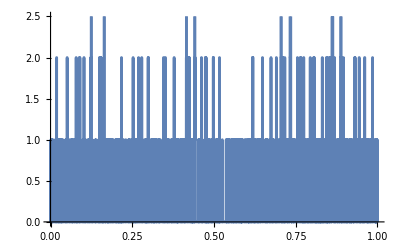
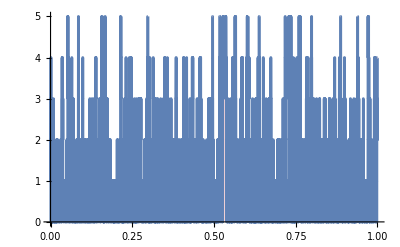
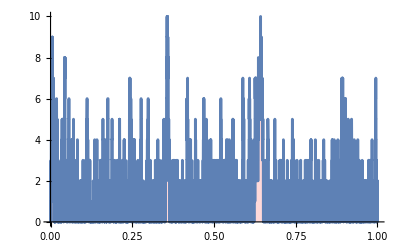
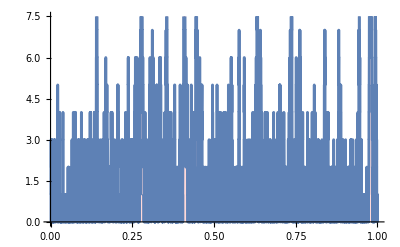
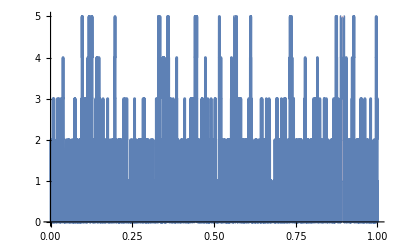
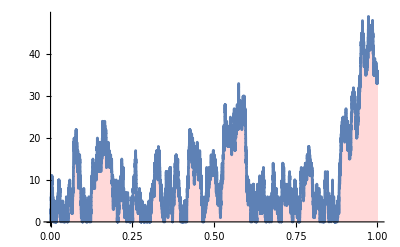
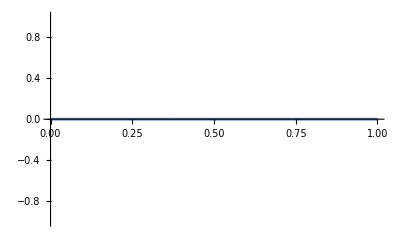
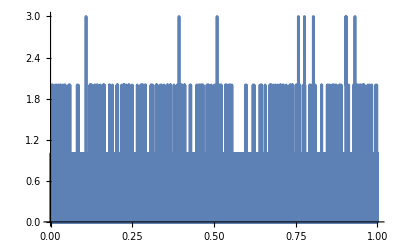

```mathematica
Table[ListLinePlot[Table[{data[[i,1]],data[[i,2,j]]},{i,Length[data]}],Filling->Axis,FillingStyle->LightRed],{j,9}]
```

```mathematica
RetardoEnlaceB = QueueProperties[{𝒩,2}, "MeanSystemTime"]//N;
RetardoEnlaceC = QueueProperties[{𝒩,3}, "MeanSystemTime"]//N;
RetardoEnlaceF = QueueProperties[{𝒩,6}, "MeanSystemTime"]//N;
RetardoEnlaceH = QueueProperties[{𝒩,8}, "MeanSystemTime"]//N;
retardoTotal = RetardoEnlaceB + RetardoEnlaceC + RetardoEnlaceF + RetardoEnlaceH
```

0.00747715

# 5.- Implementación del ejercicio con Queueing networks con protocolo S&W:

```mathematica
λ=2000; μ={3000,3000,3000,3000,3000,3000,3000,99999,99999};
```

```mathematica
γ={ (*Indicamos el caudal debido a los traficos externos que entran de forma directa*)
λ*1/4,(*Enlace A*)
λ*3/4,(*Enlace B*)
λ*1/2,(*Enlace C*)
λ*1/2,(*Enlace D*)
λ*1/3,(*Enlace E*)
λ*2/3,(*Enlace F*)
0,(*Enlace G*)
0,(*Enlace H*)
0   (*Enlace I*)
};

r={
{0,0,0,0,1/3,2/3,0,0,0}, (*Enlace A*)
{0,0,1/2,1/2,0,0,0,0,0}, (*Enlace B*)
{0,0,0,0,1/3,2/3,0,0,0}, (*Enlace C*)
{0,0,0,0,0,0,0,1,0}, (*Enlace D*)
{0,0,0,0,0,0,0,0,1}, (*Enlace E*)
{0,0,0,0,0,0,0,1,0},(*Enlace F*)
{0,0,0,0,0,0,0,0,1},(*Enlace G*)
{0,0,0,0,0,0,0,0,0},(*Enlace H*)
{0,0,0,0,0,0,0,0,0}    (*Enlace I*)
};

c={1,1,1,1,1,1,1,1,1};
```

-Graphics-      -Graphics-

```mathematica
p=0.1;
a=2;
factorSW=(1-p)/a;
factorGBN=(1-p)/(1+(a-1)*p);
muSW=factorSW*μ;
muGBN=factorGBN*μ;
```

```mathematica
𝒩SW=QueueingNetworkProcess[γ,r,muSW,c];
```

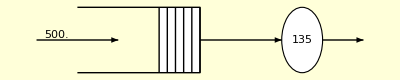
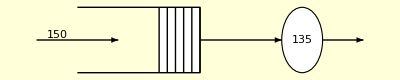
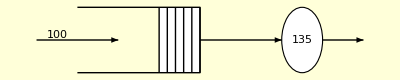
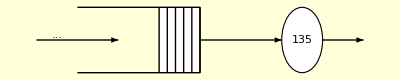
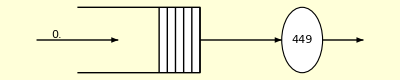
{-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 1.
Performance Measures | 
MeanSystemSize | 0.588235
MeanSystemTime | 0.00117647
MeanQueueSize | 0.217865
MeanQueueTime | 0.00043573,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 2.
Performance Measures | 
MeanSystemSize | Missing[NotAvailable]
MeanSystemTime | Missing[NotAvailable]
MeanQueueSize | Missing[NotAvailable]
MeanQueueTime | Missing[NotAvailable],-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 3.
Performance Measures | 
MeanSystemSize | Missing[NotAvailable]
MeanSystemTime | Missing[NotAvailable]
MeanQueueSize | Missing[NotAvailable]
MeanQueueTime | Missing[NotAvailable],-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 4.
Performance Measures | 
MeanSystemSize | Missing[NotAvailable]
MeanSystemTime | Missing[NotAvailable]
MeanQueueSize | Missing[NotAvailable]
MeanQueueTime | Missing[NotAvailable],-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 5.
Performance Measures | 
MeanSystemSize | Missing[NotAvailable]
MeanSystemTime | Missing[NotAvailable]
MeanQueueSize | Missing[NotAvailable]
MeanQueueTime | Missing[NotAvailable],-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 6.
Performance Measures | 
MeanSystemSize | Missing[NotAvailable]
MeanSystemTime | Missing[NotAvailable]
MeanQueueSize | Missing[NotAvailable]
MeanQueueTime | Missing[NotAvailable],-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 8.
Performance Measures | 
MeanSystemSize | 0.113403
MeanSystemTime | 0.0000247425
MeanQueueSize | 0.0115505
MeanQueueTime | 2.5201×10^-6,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 9.
Performance Measures | 
MeanSystemSize | 0.0325051
MeanSystemTime | 0.0000229448
MeanQueueSize | 0.00102332
MeanQueueTime | 7.22343×10^-7}

```mathematica
{QueueProperties[{𝒩SW,1}]//N,QueueProperties[{𝒩SW,2}]//N,QueueProperties[{𝒩SW,3}]//N,QueueProperties[{𝒩SW,4}]//N,QueueProperties[{𝒩SW,5}]//N,QueueProperties[{𝒩SW,6}]//N,QueueProperties[{𝒩SW,8}]//N,QueueProperties[{𝒩SW,9}]//N}
```

```mathematica
data=RandomFunction[𝒩SW,{0,1}]["Path"];
```

```mathematica
(*Manipulate[
Module[ {factorSW,muSW,γ,𝒩SW,data,plots},
a=2;
factorSW=(1-p)/a;
muSW=factorSW*μ;

γ={ 
λ*1/4,(*Enlace A*)
λ*3/4,(*Enlace B*)
λ*1/2,(*Enlace C*)
λ*1/2,(*Enlace D*)
λ*1/3,(*Enlace E*)
λ*2/3,(*Enlace F*)
0,(*Enlace G*)
0,(*Enlace H*)
0   (*Enlace I*)
};

𝒩SW=QueueingNetworkProcess[γ,r,muSW,c];
data=RandomFunction[𝒩SW,{0,1}]["Path"];
Table[ListLinePlot[Table[{data[[i,1]],data[[i,2,j]]},{i,Length[data]}],Filling->Axis,FillingStyle->LightRed],{j,9}]],
{λ,0.1,5,0.1},(*Control deslizante para λ*)
{p,0,1,0.01},(*Control deslizante para p*)
]
```

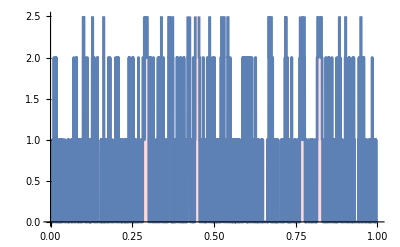
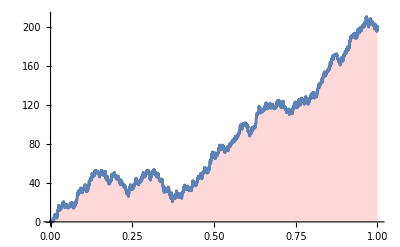
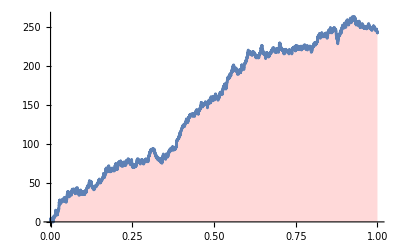
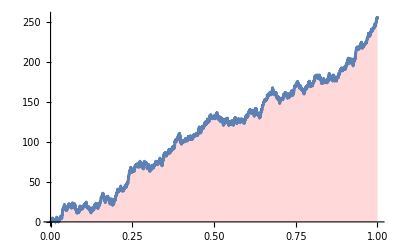
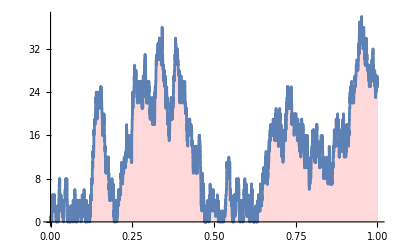
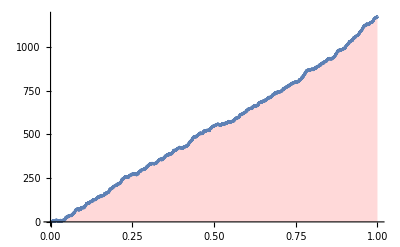
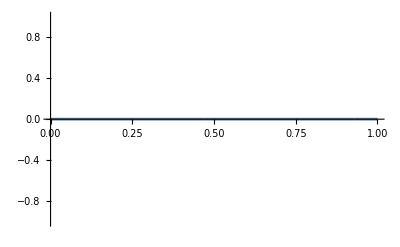
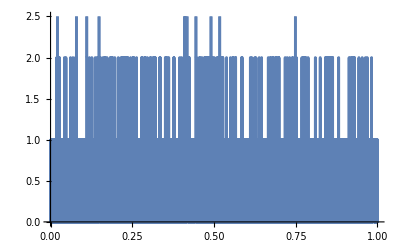

```mathematica
Table[ListLinePlot[Table[{data[[i,1]],data[[i,2,j]]},{i,Length[data]}],Filling->Axis,FillingStyle->LightRed],{j,9}]
```

```mathematica
RetardoEnlaceBSW = QueueProperties[{𝒩SW,2}, "MeanSystemTime"]//N;
RetardoEnlaceCSW = QueueProperties[{𝒩SW,3}, "MeanSystemTime"]//N;
RetardoEnlaceFSW = QueueProperties[{𝒩SW,6}, "MeanSystemTime"]//N;
RetardoEnlaceHSW = QueueProperties[{𝒩SW,8}, "MeanSystemTime"]//N;
retardoTotalSW = RetardoEnlaceBSW + RetardoEnlaceCSW + RetardoEnlaceFSW + RetardoEnlaceHSW;
```

# 6.- Implementación del ejercicio con Queueing networks con protocolo S&W:

```mathematica
λ=2000; μ={3000,3000,3000,3000,3000,3000,3000,99999,99999};
```

```mathematica
γ={ (*Indicamos el caudal debido a los traficos externos que entran de forma directa*)
λ*1/4,(*Enlace A*)
λ*3/4,(*Enlace B*)
λ*1/2,(*Enlace C*)
λ*1/2,(*Enlace D*)
λ*1/3,(*Enlace E*)
λ*2/3,(*Enlace F*)
0,(*Enlace G*)
0,(*Enlace H*)
0   (*Enlace I*)
};

r={
{0,0,0,0,1/3,2/3,0,0,0}, (*Enlace A*)
{0,0,1/2,1/2,0,0,0,0,0}, (*Enlace B*)
{0,0,0,0,1/3,2/3,0,0,0}, (*Enlace C*)
{0,0,0,0,0,0,0,1,0}, (*Enlace D*)
{0,0,0,0,0,0,0,0,1}, (*Enlace E*)
{0,0,0,0,0,0,0,1,0},(*Enlace F*)
{0,0,0,0,0,0,0,0,1},(*Enlace G*)
{0,0,0,0,0,0,0,0,0},(*Enlace H*)
{0,0,0,0,0,0,0,0,0}    (*Enlace I*)
};

c={1,1,1,1,1,1,1,1,1};
```

-Graphics-      -Graphics-

```mathematica
p=0.1;
a=2;
factorGBN=(1-p)/(1+(a-1)*p);
muGBN=factorGBN*μ;
```

```mathematica
𝒩GBN=QueueingNetworkProcess[γ,r,muGBN,c];
```

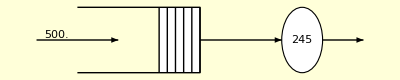
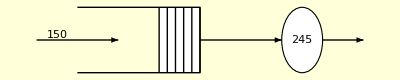
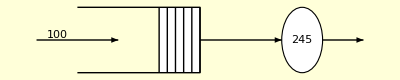
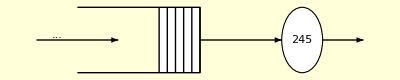
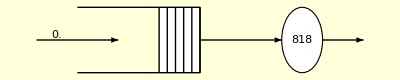
{-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 1.
Performance Measures | 
MeanSystemSize | 0.255814
MeanSystemTime | 0.000511628
MeanQueueSize | 0.0521102
MeanQueueTime | 0.00010422,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 2.
Performance Measures | 
MeanSystemSize | 1.57143
MeanSystemTime | 0.00104762
MeanQueueSize | 0.960317
MeanQueueTime | 0.000640212,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 3.
Performance Measures | 
MeanSystemSize | 2.48387
MeanSystemTime | 0.00141935
MeanQueueSize | 1.77091
MeanQueueTime | 0.00101195,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 4.
Performance Measures | 
MeanSystemSize | 2.48387
MeanSystemTime | 0.00141935
MeanQueueSize | 1.77091
MeanQueueTime | 0.00101195,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 5.
Performance Measures | 
MeanSystemSize | 1.36496
MeanSystemTime | 0.000963504
MeanQueueSize | 0.787803
MeanQueueTime | 0.000556096,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 6.
Performance Measures | 
MeanSystemSize | Missing[NotAvailable]
MeanSystemTime | Missing[NotAvailable]
MeanQueueSize | Missing[NotAvailable]
MeanQueueTime | Missing[NotAvailable],-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 8.
Performance Measures | 
MeanSystemSize | 0.0593434
MeanSystemTime | 0.0000129477
MeanQueueSize | 0.00332437
MeanQueueTime | 7.25316×10^-7,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 9.
Performance Measures | 
MeanSystemSize | 0.0176201
MeanSystemTime | 0.0000124377
MeanQueueSize | 0.000305091
MeanQueueTime | 2.15359×10^-7}

```mathematica
{QueueProperties[{𝒩GBN,1}]//N,QueueProperties[{𝒩GBN,2}]//N,QueueProperties[{𝒩GBN,3}]//N,QueueProperties[{𝒩GBN,4}]//N,QueueProperties[{𝒩GBN,5}]//N,QueueProperties[{𝒩GBN,6}]//N,QueueProperties[{𝒩GBN,8}]//N,QueueProperties[{𝒩GBN,9}]//N}
```

```mathematica
data=RandomFunction[𝒩GBN,{0,1}]["Path"];
```

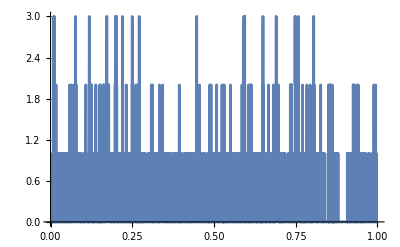
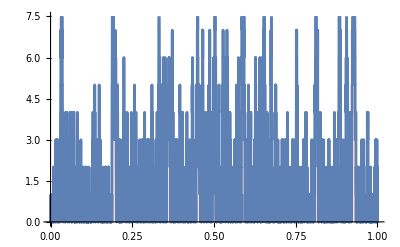
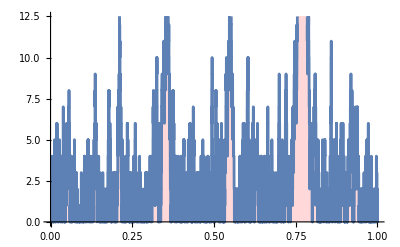
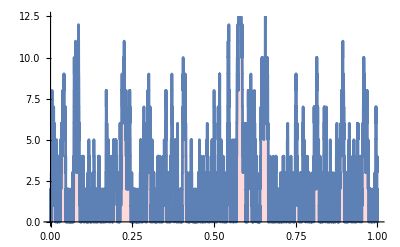
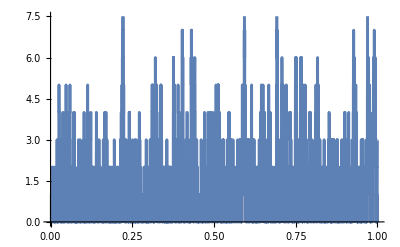
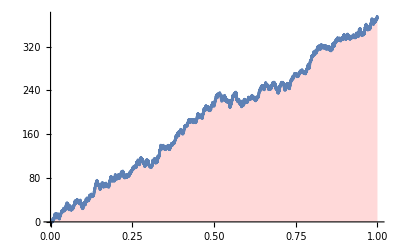
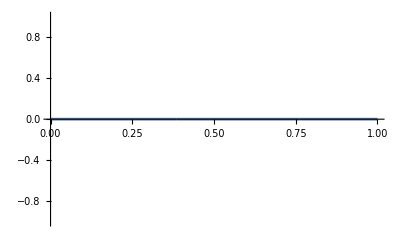
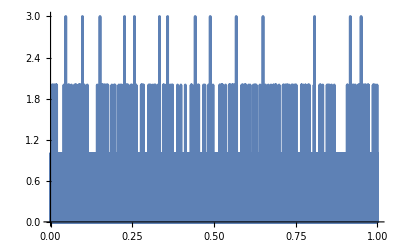

```mathematica
Table[ListLinePlot[Table[{data[[i,1]],data[[i,2,j]]},{i,Length[data]}],Filling->Axis,FillingStyle->LightRed],{j,9}]
```

```mathematica
RetardoEnlaceBGBN = QueueProperties[{𝒩GBN,2}, "MeanSystemTime"]//N;
RetardoEnlaceCGBN = QueueProperties[{𝒩GBN,3}, "MeanSystemTime"]//N;
RetardoEnlaceFGBN = QueueProperties[{𝒩GBN,6}, "MeanSystemTime"]//N;
RetardoEnlaceHGBN = QueueProperties[{𝒩GBN,8}, "MeanSystemTime"]//N;
retardoTotalGBN = RetardoEnlaceBGBN + RetardoEnlaceCGBN + RetardoEnlaceFGBN + RetardoEnlaceHGBN //N
```

0.00247992+QueueProperties[{QueueingNetworkProcess[{500.,1500.,1000.,1000.,666.667,1333.33,0.,0.,0.},{{0.,0.,0.,0.,0.333333,0.666667,0.,0.,0.},{0.,0.,0.5,0.5,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.333333,0.666667,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.},{0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.}},{2454.55,2454.55,2454.55,2454.55,2454.55,2454.55,2454.55,81817.4,81817.4},{1.,1.,1.,1.,1.,1.,1.,1.,1.}],6.},MeanSystemTime]